a) Potential

```mathematica
Clear["Global`*"]
```

```mathematica
L=1; Vo =25;
```

```mathematica
V[x_]:= -Vo/2 (1+Cos[2Pi x/L]) /; Abs[x] ≤ L/2
```

```mathematica
V[x_]:= 0 /; Abs[x] > L/2
```

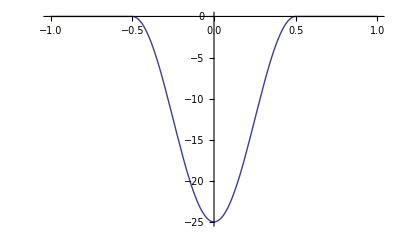

```mathematica
Plot[V[x],{x,-L,L}]
```

## b) EigenValue / Eigenfunction (Even)

```mathematica
B = 1;
ψ1[x_] := A Exp[ Abs[2 en]^(1/2) x]
ψ3[x_] := B Exp[- Abs[2 en]^(1/2) x]
```

```mathematica
eqn[en_] := ψ2''[x] + 2(en - V[x])ψ2[x]
```

```mathematica
wavefunc2[energy_] :=(en = energy; NDSolve[{ eqn[energy] == 0, ψ2[-L/2] ==  ψ1[-L/2], 
					ψ2'[-L/2] ==  ψ1'[-L/2]}, 
		ψ2, {x, -L/2, 0} ])
```

```mathematica
sol2[x_?NumericQ, en_?NumericQ] := ψ2[x] /. wavefunc2[en][[1]]
```

```mathematica
sol2prime[x_?NumericQ,en_?NumericQ]:=ψ2'[x]/.wavefunc2[en][[1]]
```

```mathematica
A=B;
```

```mathematica
eval = energy /. FindRoot [ sol2prime[0, energy],{energy, -5, -25} ]
```

-15.329

Energy ground state = -15.32

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2
```

```mathematica
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0
```

```mathematica
ψnn[x_] := ψ1[x] /; x < -L/2
```

```mathematica
ψnn [x_] := ψ3[x] /; x > L/2
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

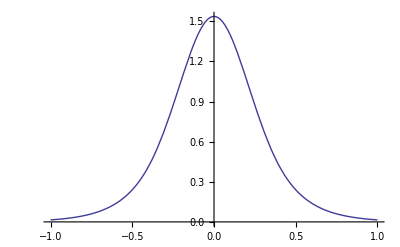

```mathematica
Plot[ψ[x],{x,-L,L}]
```

## c) EigenValue / Eigenfunction (Odd)

```mathematica
A=-B;
```

```mathematica
eval = en /. FindRoot [sol2[0, en] ,{en, -0.5, -25} ]
```

-0.92539

Energy  state of 1 = -15.32

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := -efunc2[-x] /; 0 ≤  x  ≤  L/2
```

```mathematica
normconst = Sqrt[NIntegrate [ ψnn[x]^2, {x, -Infinity,Infinity} ] ];
```

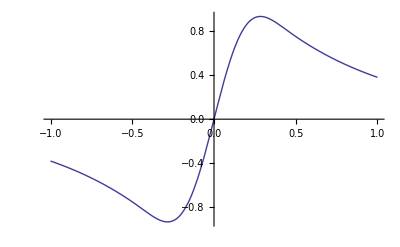

```mathematica
Plot[ψ[x],{x,-L,L}]
```

## d) Moar Bound States

```mathematica
Clear[A,B,eval]
```

```mathematica
Vo=250;B=1;A=B;
```

```mathematica
eval = energy /. FindRoot [ sol2prime[0, energy],{energy, -20, -50} ]
```

-92.5528

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2
```

```mathematica
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0
```

```mathematica
ψnn[x_] := ψ1[x] /; x < -L/2
```

```mathematica
ψnn [x_] := ψ3[x] /; x > L/2
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

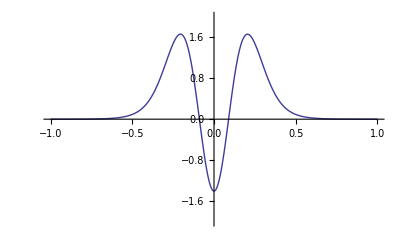

```mathematica
Plot[ψ[x],{x,-L,L},PlotRange->{-2,2}]
```

After a couple of attempts Vo around 150 gives even parity wavefunction (2 nodes) that is 6 x the original potential